```mathematica
export[name_]:=Export["/home/rhennigan/code/classes/cs546/pa2/objects/"<>name<>".obj",ExampleData[{"Geometry3D",name}]]
```

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
ExampleData[{"Geometry3D","Cone"}]
```

```mathematica
lineCount[model_]:=Module[
{polygons,lines},
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
lines=Union[Sort/@Flatten[Partition[#,2,1,1]&/@polygons,1]];
Length[lines]
]
```

```mathematica
{#,lineCount[#]}&/@ExampleData["Geometry3D"]⟦All,2⟧
```

{{BassGuitar,3600},{Beethoven,6090},{CastleWall,8177},{Cone,758},{Cow,8706},{Deimos,28224},{Galleon,6146},{HammerheadShark,5365},{Horse,14543},{KleinBottle,6101},{MoebiusStrip,528},{Phobos,28224},{PottedPlant,18548},{Seashell,2594},{SedanCar,15397},{SpaceShuttle,701},{StanfordBunny,104288},{Torus,13186},{Tree,32528},{Triceratops,5664},{Tugboat,72765},{UtahTeapot,928},{UtahVWBug,2277},{Vase,20403},{VikingLander,32155},{Wrench,6114},{Zeppelin,5083}}

```mathematica
lineCounts=%;
```

```mathematica
"<option value=\""<>#⟦1⟧<>"\">"<>#⟦1⟧<>" ("<>ToString[#⟦2⟧]<>" lines)</option>\n"&/@lineCounts//StringJoin
```

<option value="BassGuitar">BassGuitar (3600 lines)</option>
<option value="Beethoven">Beethoven (6090 lines)</option>
<option value="CastleWall">CastleWall (8177 lines)</option>
<option value="Cone">Cone (758 lines)</option>
<option value="Cow">Cow (8706 lines)</option>
<option value="Deimos">Deimos (28224 lines)</option>
<option value="Galleon">Galleon (6146 lines)</option>
<option value="HammerheadShark">HammerheadShark (5365 lines)</option>
<option value="Horse">Horse (14543 lines)</option>
<option value="KleinBottle">KleinBottle (6101 lines)</option>
<option value="MoebiusStrip">MoebiusStrip (528 lines)</option>
<option value="Phobos">Phobos (28224 lines)</option>
<option value="PottedPlant">PottedPlant (18548 lines)</option>
<option value="Seashell">Seashell (2594 lines)</option>
<option value="SedanCar">SedanCar (15397 lines)</option>
<option value="SpaceShuttle">SpaceShuttle (701 lines)</option>
<option value="StanfordBunny">StanfordBunny (104288 lines)</option>
<option value="Torus">Torus (13186 lines)</option>
<option value="Tree">Tree (32528 lines)</option>
<option value="Triceratops">Triceratops (5664 lines)</option>
<option value="Tugboat">Tugboat (72765 lines)</option>
<option value="UtahTeapot">UtahTeapot (928 lines)</option>
<option value="UtahVWBug">UtahVWBug (2277 lines)</option>
<option value="Vase">Vase (20403 lines)</option>
<option value="VikingLander">VikingLander (32155 lines)</option>
<option value="Wrench">Wrench (6114 lines)</option>
<option value="Zeppelin">Zeppelin (5083 lines)</option>

```mathematica
{#⟦1⟧,Which[#⟦2⟧>14543,"***",#⟦2⟧>5365,"**",True,"*"]}&/@lineCounts
```

{{BassGuitar,*},{Beethoven,**},{CastleWall,**},{Cone,*},{Cow,**},{Deimos,***},{Galleon,**},{HammerheadShark,*},{Horse,**},{KleinBottle,**},{MoebiusStrip,*},{Phobos,***},{PottedPlant,***},{Seashell,*},{SedanCar,***},{SpaceShuttle,*},{StanfordBunny,***},{Torus,**},{Tree,***},{Triceratops,**},{Tugboat,***},{UtahTeapot,*},{UtahVWBug,*},{Vase,***},{VikingLander,***},{Wrench,**},{Zeppelin,*}}

```mathematica
SortBy[lineCounts,Last]
```

{{MoebiusStrip,528},{SpaceShuttle,701},{Cone,758},{UtahTeapot,928},{UtahVWBug,2277},{Seashell,2594},{BassGuitar,3600},{Zeppelin,5083},{HammerheadShark,5365},{Triceratops,5664},{Beethoven,6090},{KleinBottle,6101},{Wrench,6114},{Galleon,6146},{CastleWall,8177},{Cow,8706},{Torus,13186},{Horse,14543},{SedanCar,15397},{PottedPlant,18548},{Vase,20403},{Deimos,28224},{Phobos,28224},{VikingLander,32155},{Tree,32528},{Tugboat,72765},{StanfordBunny,104288}}

```mathematica
min=Min[SortBy[lineCounts,Last]⟦All,2⟧]
max=Max[SortBy[lineCounts,Last]⟦All,2⟧]
```

528

104288

```mathematica
min+.25(max-min)
```

26468.

```mathematica
Quantile[SortBy[lineCounts,Last]⟦All,2⟧,.33]
Quantile[SortBy[lineCounts,Last]⟦All,2⟧,.66]
```

5365

14543

```mathematica
ClusteringComponents[SortBy[lineCounts,Last]⟦All,2⟧]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2}

```mathematica
export/@ExampleData["Geometry3D"]⟦All,2⟧
```

{/home/rhennigan/code/classes/cs546/pa2/objects/BassGuitar.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Beethoven.obj,/home/rhennigan/code/classes/cs546/pa2/objects/CastleWall.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Cone.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Cow.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Deimos.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Galleon.obj,/home/rhennigan/code/classes/cs546/pa2/objects/HammerheadShark.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Horse.obj,/home/rhennigan/code/classes/cs546/pa2/objects/KleinBottle.obj,/home/rhennigan/code/classes/cs546/pa2/objects/MoebiusStrip.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Phobos.obj,/home/rhennigan/code/classes/cs546/pa2/objects/PottedPlant.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Seashell.obj,/home/rhennigan/code/classes/cs546/pa2/objects/SedanCar.obj,/home/rhennigan/code/classes/cs546/pa2/objects/SpaceShuttle.obj,/home/rhennigan/code/classes/cs546/pa2/objects/StanfordBunny.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Torus.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Tree.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Triceratops.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Tugboat.obj,/home/rhennigan/code/classes/cs546/pa2/objects/UtahTeapot.obj,/home/rhennigan/code/classes/cs546/pa2/objects/UtahVWBug.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Vase.obj,/home/rhennigan/code/classes/cs546/pa2/objects/VikingLander.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Wrench.obj,/home/rhennigan/code/classes/cs546/pa2/objects/Zeppelin.obj}

```mathematica
export["SedanCar"]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\StanfordBunny.obj

```mathematica
model="Horse";
vertices=Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
```

```mathematica
ExampleData[{"Geometry3D",model},"Properties"]
```

{Graphics3D,GraphicsComplex,Name,PolygonCount,PolygonData,PolygonObjects,VertexData,VertexNormals}

```mathematica
model="Horse";
```

```mathematica
size=500.0;
model="UtahTeapot";
vertices=size*Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
gc=ExampleData[{"Geometry3D",model},"GraphicsComplex"];
gc⟦1⟧=Rescale[vertices];
Export["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj",Graphics3D[gc]]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahTeapot.obj

```mathematica
Graphics3D[gc,Axes->True]
```

-Graphics3D-

```mathematica
Import["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj"]
```

-Graphics3D-

```mathematica
{{rx1,rx2},{ry1,ry2},{rz1,rz2}}={Min[#],Max[#]}&/@Transpose[vertices]
```

{{67.3118,500.},{0.,269.247},{215.411,417.347}}

```mathematica
rx=rx2-rx1
ry=ry2-ry1
rz=rz2-rz1
```

432.688

269.247

201.936

```mathematica
rm=Max[rx,ry,rz]
```

432.688

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\UtahTeapot.obj",ExampleData[{"Geometry3D","UtahTeapot"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\UtahTeapot.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\SpaceShuttle.obj",ExampleData[{"Geometry3D","SpaceShuttle"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\SpaceShuttle.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\BassGuitar.obj",ExampleData[{"Geometry3D","BassGuitar"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\BassGuitar.obj

```mathematica
Union[Length/@polygons]
```

{3,4}

```mathematica
FullSimplify[RotationMatrix[tyz,{1,0,0}].(RotationMatrix[txz,{0,1,0}].(RotationMatrix[txy,{0,0,1}].{x,y,z})),Element[{tyz,txz,txy,x,y,z},Reals]]
```

{x Cos[txy] Cos[txz]-y Cos[txz] Sin[txy]+z Sin[txz],x Cos[tyz] Sin[txy]-(z Cos[txz]+y Sin[txy] Sin[txz]) Sin[tyz]+Cos[txy] (y Cos[tyz]+x Sin[txz] Sin[tyz]),z Cos[txz] Cos[tyz]+Cos[tyz] (-x Cos[txy]+y Sin[txy]) Sin[txz]+(y Cos[txy]+x Sin[txy]) Sin[tyz]}

```mathematica
exp=Expand@FullSimplify[{x Cos[txy] Cos[txz]-y Cos[txz] Sin[txy]+z Sin[txz],x Cos[tyz] Sin[txy]-(z Cos[txz]+y Sin[txy] Sin[txz]) Sin[tyz]+Cos[txy] (y Cos[tyz]+x Sin[txz] Sin[tyz]),z Cos[txz] Cos[tyz]+Cos[tyz] (-x Cos[txy]+y Sin[txy]) Sin[txz]+(y Cos[txy]+x Sin[txy]) Sin[tyz]}/.{x->x-size/2,y->y-size/2,z->z-size/2},Element[{size,ctyz,ctxz,ctxy,styz,stxz,stxy,x,y,z},Reals]]
```

{-1/2 size Cos[txy] Cos[txz]+x Cos[txy] Cos[txz]+1/2 size Cos[txz] Sin[txy]-y Cos[txz] Sin[txy]-1/2 size Sin[txz]+z Sin[txz],-1/2 size Cos[txy] Cos[tyz]+y Cos[txy] Cos[tyz]-1/2 size Cos[tyz] Sin[txy]+x Cos[tyz] Sin[txy]+1/2 size Cos[txz] Sin[tyz]-z Cos[txz] Sin[tyz]-1/2 size Cos[txy] Sin[txz] Sin[tyz]+x Cos[txy] Sin[txz] Sin[tyz]+1/2 size Sin[txy] Sin[txz] Sin[tyz]-y Sin[txy] Sin[txz] Sin[tyz],-1/2 size Cos[txz] Cos[tyz]+z Cos[txz] Cos[tyz]+1/2 size Cos[txy] Cos[tyz] Sin[txz]-x Cos[txy] Cos[tyz] Sin[txz]-1/2 size Cos[tyz] Sin[txy] Sin[txz]+y Cos[tyz] Sin[txy] Sin[txz]-1/2 size Cos[txy] Sin[tyz]+y Cos[txy] Sin[tyz]-1/2 size Sin[txy] Sin[tyz]+x Sin[txy] Sin[tyz]}

```mathematica
Depth[txy]
```

1

```mathematica
StringReplace[ToString[Cos[txy]],{"Cos["->"c","]"->""}]
```

ctxy

```mathematica
"Cos[txy]"
```

```mathematica
factorTerms[exp_]:=SortBy[Select[Tally[First[Last[Reap[Map[Sow,exp,Infinity]]]]],Depth[#⟦1⟧]>1&],-Last[#]&]
```

```mathematica
inReals[exp_]:=Element[Union[Cases[exp,_Symbol,Infinity]],Reals]
```

```mathematica
factorTerms[exp]
```

{{Cos[txy],10},{Cos[tyz],10},{Sin[txy],10},{Sin[txz],10},{Sin[tyz],10},{Cos[txz],8},{-1/2 size Cos[txy] Cos[txz],1},{x Cos[txy] Cos[txz],1},{-1/2 size Cos[txy] Cos[tyz],1},{y Cos[txy] Cos[tyz],1},{-1/2 size Cos[txz] Cos[tyz],1},{z Cos[txz] Cos[tyz],1},{1/2 size Cos[txz] Sin[txy],1},{-y Cos[txz] Sin[txy],1},{-1/2 size Cos[tyz] Sin[txy],1},{x Cos[tyz] Sin[txy],1},{-1/2 size Sin[txz],1},{z Sin[txz],1},{1/2 size Cos[txy] Cos[tyz] Sin[txz],1},{-x Cos[txy] Cos[tyz] Sin[txz],1},{-1/2 size Cos[tyz] Sin[txy] Sin[txz],1},{y Cos[tyz] Sin[txy] Sin[txz],1},{-1/2 size Cos[txy] Cos[txz]+x Cos[txy] Cos[txz]+1/2 size Cos[txz] Sin[txy]-y Cos[txz] Sin[txy]-1/2 size Sin[txz]+z Sin[txz],1},{-1/2 size Cos[txy] Sin[tyz],1},{y Cos[txy] Sin[tyz],1},{1/2 size Cos[txz] Sin[tyz],1},{-z Cos[txz] Sin[tyz],1},{-1/2 size Sin[txy] Sin[tyz],1},{x Sin[txy] Sin[tyz],1},{-1/2 size Cos[txy] Sin[txz] Sin[tyz],1},{x Cos[txy] Sin[txz] Sin[tyz],1},{1/2 size Sin[txy] Sin[txz] Sin[tyz],1},{-y Sin[txy] Sin[txz] Sin[tyz],1},{-1/2 size Cos[txz] Cos[tyz]+z Cos[txz] Cos[tyz]+1/2 size Cos[txy] Cos[tyz] Sin[txz]-x Cos[txy] Cos[tyz] Sin[txz]-1/2 size Cos[tyz] Sin[txy] Sin[txz]+y Cos[tyz] Sin[txy] Sin[txz]-1/2 size Cos[txy] Sin[tyz]+y Cos[txy] Sin[tyz]-1/2 size Sin[txy] Sin[tyz]+x Sin[txy] Sin[tyz],1},{-1/2 size Cos[txy] Cos[tyz]+y Cos[txy] Cos[tyz]-1/2 size Cos[tyz] Sin[txy]+x Cos[tyz] Sin[txy]+1/2 size Cos[txz] Sin[tyz]-z Cos[txz] Sin[tyz]-1/2 size Cos[txy] Sin[txz] Sin[tyz]+x Cos[txy] Sin[txz] Sin[tyz]+1/2 size Sin[txy] Sin[txz] Sin[tyz]-y Sin[txy] Sin[txz] Sin[tyz],1}}

```mathematica
exp2=FullSimplify[exp/.{
Cos[tyz]->ctyz,
Cos[txz]->ctxz,
Cos[txy]->ctxy,
Sin[tyz]->styz,
Sin[txz]->stxz,
Sin[txy]->stxy
},inReals[exp]]
```

{1/2 (-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z)),1/2 (-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z))),1/2 (-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z))}

```mathematica
factorTerms[exp2]
```

{{size-2 x,5},{-2 x,5},{size-2 y,5},{-2 y,5},{size-2 z,3},{-2 z,3},{-ctxy ctxz (size-2 x),1},{-ctyz stxy (size-2 x),1},{ctyz stxz (size-2 x),1},{styz (size-2 x),1},{stxz styz (size-2 x),1},{stxz styz (size-2 x)+ctyz (size-2 y),1},{-ctxy (stxz styz (size-2 x)+ctyz (size-2 y)),1},{styz (size-2 x)+ctyz stxz (size-2 y),1},{-stxy (styz (size-2 x)+ctyz stxz (size-2 y)),1},{ctyz stxz (size-2 x)-styz (size-2 y),1},{ctxy (ctyz stxz (size-2 x)-styz (size-2 y)),1},{ctyz (size-2 y),1},{ctxz stxy (size-2 y),1},{ctyz stxz (size-2 y),1},{stxy stxz (size-2 y),1},{-styz (size-2 y),1},{1/2 (-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z))),1},{-ctyz stxy (size-2 x)-ctxy (stxz styz (size-2 x)+ctyz (size-2 y))+styz (stxy stxz (size-2 y)+ctxz (size-2 z)),1},{stxy stxz (size-2 y)+ctxz (size-2 z),1},{styz (stxy stxz (size-2 y)+ctxz (size-2 z)),1},{1/2 (-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z)),1},{-stxy (styz (size-2 x)+ctyz stxz (size-2 y))+ctxy (ctyz stxz (size-2 x)-styz (size-2 y))-ctxz ctyz (size-2 z),1},{1/2 (-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z)),1},{-ctxy ctxz (size-2 x)+ctxz stxy (size-2 y)-stxz (size-2 z),1},{ctxz (size-2 z),1},{-ctxz ctyz (size-2 z),1},{-stxz (size-2 z),1}}

```mathematica
ClearAll[size]
```

```mathematica
exp3=FullSimplify[exp2/.{
(size-2 x)->s2x,
(size-2 y)->s2y,
(size-2 z)->s2z
},inReals[exp2]]
```

{1/2 (-ctxy ctxz s2x+ctxz s2y stxy-s2z stxz),1/2 (-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),-1/2 ctyz (ctxz s2z-ctxy s2x stxz+s2y stxy stxz)-1/2 (ctxy s2y+s2x stxy) styz}

```mathematica
exp4={
1/2 (-ctxy ctxz s2x+ctxz s2y stxy-s2z stxz)+size/2,
1/2 (-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz))+size/2,
-1/2 ctyz (ctxz s2z-ctxy s2x stxz+s2y stxy stxz)-1/2 (ctxy s2y+s2x stxy) styz+size/2
};
exp4=FullSimplify[exp4,inReals[exp4]]
```

{1/2 (-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz),1/2 (size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),1/2 (-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz)}

```mathematica
factorTerms[exp4]
```

{{ctxy s2x,1},{-ctxy ctxz s2x,1},{ctxy s2y,1},{ctyz s2y,1},{-ctxz ctyz s2z,1},{s2x stxy,1},{-ctyz s2x stxy,1},{-s2y stxy,1},{ctxz s2y stxy,1},{ctxy s2y+s2x stxy,1},{ctxy s2x-s2y stxy,1},{-s2z stxz,1},{ctyz (ctxy s2x-s2y stxy) stxz,1},{1/2 (-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz),1},{-ctxy ctxz s2x+size+ctxz s2y stxy-s2z stxz,1},{ctxz s2z styz,1},{-(ctxy s2y+s2x stxy) styz,1},{s2x stxz styz,1},{s2y stxy stxz styz,1},{1/2 (-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz),1},{-ctxz ctyz s2z+size+ctyz (ctxy s2x-s2y stxy) stxz-(ctxy s2y+s2x stxy) styz,1},{ctyz s2y+s2x stxz styz,1},{-ctxy (ctyz s2y+s2x stxz styz),1},{1/2 (size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz)),1},{size-ctyz s2x stxy+ctxz s2z styz+s2y stxy stxz styz-ctxy (ctyz s2y+s2x stxz styz),1}}

```mathematica
CForm[exp4⟦1⟧]
```

(-(ctxy*ctxz*s2x) + size + ctxz*s2y*stxy - s2z*stxz)/2.

```mathematica
CForm[exp4⟦2⟧]
```

(size - ctyz*s2x*stxy + ctxz*s2z*styz + s2y*stxy*stxz*styz - ctxy*(ctyz*s2y + s2x*stxz*styz))/2.

```mathematica
CForm[exp4⟦3⟧]
```

(-(ctxz*ctyz*s2z) + size + ctyz*(ctxy*s2x - s2y*stxy)*stxz - (ctxy*s2y + s2x*stxy)*styz)/2.

```mathematica
cases[term_]:=Cases[exp,term,Infinity]
```

```mathematica
cases[size/2]
```

{-size/2,-size/2}

```mathematica
FullSimplify[exp/.{
Cos[tyz]->ctyz,
Cos[txz]->ctxz,
Cos[txy]->ctxy,
Sin[tyz]->styz,
Sin[txz]->stxz,
Sin[txy]->stxy
},Element[{ctyz,ctxz,ctxy,styz,stxz,stxy,x,y,z},Reals]]
```

{ctxy ctxz x-ctxz stxy y+stxz z,ctyz stxy x+ctxy stxz styz x+ctxy ctyz y-stxy stxz styz y-ctxz styz z,-ctxy ctyz stxz x+stxy styz x+ctyz stxy stxz y+ctxy styz y+ctxz ctyz z}

```mathematica
CForm[%]
```

List(ctxy*ctxz*x - ctxz*stxy*y + stxz*z,ctyz*stxy*x + ctxy*stxz*styz*x + ctxy*ctyz*y - stxy*stxz*styz*y - 
    ctxz*styz*z,-(ctxy*ctyz*stxz*x) + stxy*styz*x + ctyz*stxy*stxz*y + ctxy*styz*y + ctxz*ctyz*z)

```mathematica
cases[Cos[tyz]]
cases[Cos[txz]]
cases[Cos[txy]]
```

{Cos[tyz],Cos[tyz],Cos[tyz],Cos[tyz]}

{Cos[txz],Cos[txz],Cos[txz],Cos[txz]}

{Cos[txy],Cos[txy],Cos[txy],Cos[txy]}

```mathematica
cases[Sin[txy]]
cases[Sin[txz]]
cases[Sin[txy]]
```

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

{Sin[txz],Sin[txz],Sin[txz],Sin[txz]}

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

```mathematica
cases[Cos[txz]]
```

{Cos[txz],Cos[txz],Cos[txz],Cos[txz]}

```mathematica
cases[Sin[txy]]
```

{Sin[txy],Sin[txy],Sin[txy],Sin[txy],Sin[txy]}

```mathematica
cases[Sin[txz]]
```

{Sin[txz],Sin[txz],Sin[txz],Sin[txz]}

```mathematica
%//CForm
```

List(x*Cos(txy)*Cos(txz) - y*Cos(txz)*Sin(txy) + z*Sin(txz),
   x*Cos(tyz)*Sin(txy) - (z*Cos(txz) + y*Sin(txy)*Sin(txz))*Sin(tyz) + 
    Cos(txy)*(y*Cos(tyz) + x*Sin(txz)*Sin(tyz)),
   z*Cos(txz)*Cos(tyz) + Cos(tyz)*(-(x*Cos(txy)) + y*Sin(txy))*Sin(txz) + (y*Cos(txy) + x*Sin(txy))*Sin(tyz))

```mathematica
{x Cos[t]-y Sin[t],y Cos[t]+x Sin[t],z}//CForm
```

List(x*Cos(t) - y*Sin(t),y*Cos(t) + x*Sin(t),z)

```mathematica
size=500.0;
model="UtahTeapot";
vertices=size*Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
lines=Union[Sort/@Flatten[Partition[#,2,1,1]&/@polygons,1]];
```

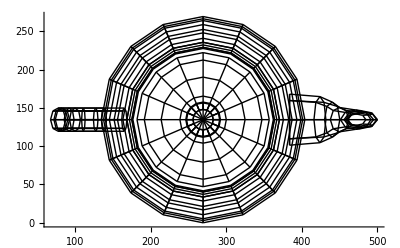

```mathematica
xy=Graphics[GraphicsComplex[vertices⟦All,{1,2}⟧,Line/@lines],Axes->True]
```

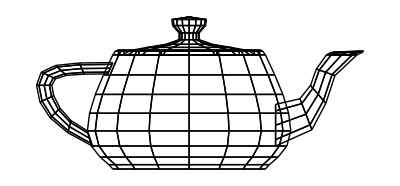

```mathematica
xz=Graphics[GraphicsComplex[vertices⟦All,{1,3}⟧,Line/@lines]]
```

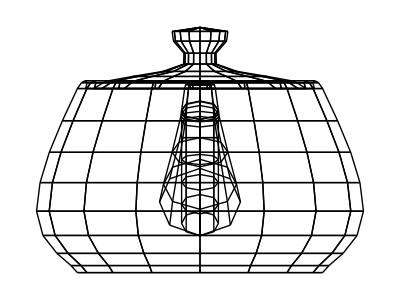

```mathematica
yz=Graphics[GraphicsComplex[vertices⟦All,{2,3}⟧,Line/@lines]]
```

```mathematica
isoMatrix=FullSimplify[({{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}}).({{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}}),Element[{α,β},Reals]]
```

{{Cos[β],0,-Sin[β]},{Sin[α] Sin[β],Cos[α],Cos[β] Sin[α]},{Cos[α] Sin[β],-Sin[α],Cos[α] Cos[β]}}

```mathematica
FullSimplify[(isoMatrix.{x,y,z})/.{
α->ArcSin[Tan[Pi/6]],
β->Pi/4
},Element[{α,β,x,y,z},Reals]]⟦1;;2⟧
```

{(x-z)/(√2),(x+2 y+z)/(√6)}

```mathematica
isoProject[{x_,z_,y_}]:={(x-z)/(√2),(x+2 y+z)/(√6)}
```

```mathematica
isoProject[{x,y,z}]//CForm
```

List((x - y)/Sqrt(2),(x + y + 2*z)/Sqrt(6))

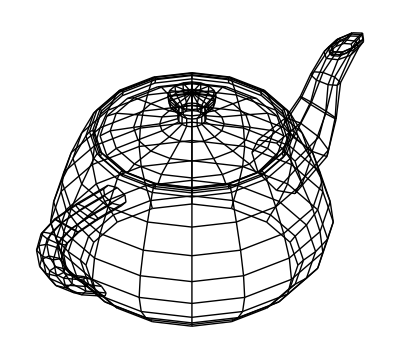

```mathematica
yz=Graphics[GraphicsComplex[isoProject/@vertices,Line/@lines]]
```

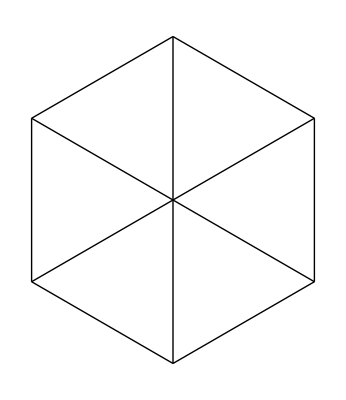

```mathematica
Graphics[Line/@Map[isoProject,Cube,{2}]]
```

```mathematica
fov=90.0;
aspect=1.0;
nearDist=1.0;
farDist=2.0;
leftHanded=True;
```

```mathematica
projMatrix[fov_,aspect_,nearDist_,farDist_,leftHanded_]:=Module[
{frustumDepth,oneOverDepth,r11,r00,r22,r32,r23,r33},
frustumDepth=farDist-nearDist;
oneOverDepth=1/frustumDepth;
r11=1.0 / Tan[0.5*fov];
r00=If[leftHanded,1,-1]*r11/aspect;
r22=farDist*oneOverDepth;
r32=(-farDist*nearDist)*oneOverDepth;
r23=1.0;
r33=0.0;
({{r00, 0.0, 0.0, 0.0}, {0.0, r11, 0.0, 0.0}, {0.0, 0.0, r22, r23}, {0.0, 0.0, r32, r33}})
]
```

```mathematica
m=projMatrix[75,1.0,-1.0,2.0,True]
```

{{-4.95576,0.,0.,0.},{0.,-4.95576,0.,0.},{0.,0.,0.666667,1.},{0.,0.,0.666667,0.}}

```mathematica
{xc,yc,zc,wc}=FullSimplify[Chop[m.{x,y,z,1.0}],Element[{x,y,z},Reals]]
```

{-4.95576 x,-4.95576 y,1.+0.666667 z,0.666667 z}

```mathematica
With[{ex={xc,yc}/wc},
f=Compile[{{pt,_Real,1}},
Block[{x,y,z},
{x,y,z}=pt⟦1;;3⟧;
ex
],RuntimeAttributes->{Listable}]]
```

CompiledFunction[…]

```mathematica
mv=Module[{mean=Mean[vertices]},#-mean&/@vertices];
```

```mathematica
Graphics[GraphicsComplex[f[vertices],Line/@lines],Axes->True,PlotRange->All]
```

```mathematica
IncDim[sg_,d_]:=Map[Append[#,d]&,sg,{2}]

DblSegments[l_]:=Join[IncDim[l,-1],IncDim[l,1]]

ConnectPoints[l1_,l2_]:=Table[{Flatten[l1,1][[i]],Flatten[l2,1][[i]]},{i,Length[Flatten[l1,1]]}]

DblConnSegments[l_]:=Union[ConnectPoints[IncDim[l,-1],IncDim[l,1]]]

UpDimShape[l_]:=Join[DblSegments[l],DblConnSegments[l]]

Sqr=UpDimShape[{{{-1},{1}}}];

Cube=UpDimShape[Sqr];

Rx[θ_]:={{1,0,0,0},{0,Cos[θ],-Sin[θ],0},{0,Sin[θ],Cos[θ],0},{0,0,0,1}};

Ry[θ_]:={{Cos[θ],0,Sin[θ],0},{0,1,0,0},{-Sin[θ],0,Cos[θ],0},{0,0,0,1}};

Rz[θ_]:={{Cos[θ],-Sin[θ],0,0},{Sin[θ],Cos[θ],0,0},{0,0,1,0},{0,0,0,1}};

Homogen[l_]:=Map[Append[#,1]&,l,{2}]

RotateX[l_,θ_]:=Map[Rx[θ].#&,l,{2}]
RotateY[l_,θ_]:=Map[Ry[θ].#&,l,{2}]
RotateZ[l_,θ_]:=Map[Rz[θ].#&,l,{2}]

DropUnit[l_]:=Map[Drop[#,-1]&,l,{2}]

RotFigure[l_,θx_,θy_,θz_]:=DropUnit[RotateZ[RotateY[RotateX[Homogen[l],θx],θy],θz]]

Mtr[x_,y_,z_]:={{1,0,0,x},{0,1,0,y},{0,0,1,z},{0,0,0,1}}

Trans4vec[l_,x_,y_,z_]:=Map[Mtr[x,y,z].#&,l,{2}]

Trans[l_,x_,y_,z_]:=DropUnit[Trans4vec[Homogen[l],x,y,z]]

Ortho[l_]:=Map[Drop[#,-1]&,l,{2}]

PersPoint[pt_,d_]:=Map[#/(Last[pt]/d)&,pt]

Perspective[l_,d_]:=Ortho[Map[PersPoint[#,d]&,l,{2}]]
```

```mathematica
exp1=Perspective[Trans[RotFigure[{{{x1,y1,z1},{x2,y2,z2}}},txy,txz,tyz],0,0,-1000],-1];
```

```mathematica
exp2=FullSimplify[exp1,inReals[exp1]]
```

{{{(x1 Cos[txz] Cos[tyz]+Cos[tyz] (z1 Cos[txy]+y1 Sin[txy]) Sin[txz]+(-y1 Cos[txy]+z1 Sin[txy]) Sin[tyz])/(3-Cos[txz] (z1 Cos[txy]+y1 Sin[txy])+x1 Sin[txz]),(Cos[tyz] (y1 Cos[txy]-z1 Sin[txy])+(x1 Cos[txz]+(z1 Cos[txy]+y1 Sin[txy]) Sin[txz]) Sin[tyz])/(3-Cos[txz] (z1 Cos[txy]+y1 Sin[txy])+x1 Sin[txz])},{(x2 Cos[txz] Cos[tyz]+Cos[tyz] (z2 Cos[txy]+y2 Sin[txy]) Sin[txz]+(-y2 Cos[txy]+z2 Sin[txy]) Sin[tyz])/(3-Cos[txz] (z2 Cos[txy]+y2 Sin[txy])+x2 Sin[txz]),(Cos[tyz] (y2 Cos[txy]-z2 Sin[txy])+(x2 Cos[txz]+(z2 Cos[txy]+y2 Sin[txy]) Sin[txz]) Sin[tyz])/(3-Cos[txz] (z2 Cos[txy]+y2 Sin[txy])+x2 Sin[txz])}}}

```mathematica
factorTerms[exp2]⟦;;8⟧
```

{{Cos[txy],12},{Sin[txy],12},{Cos[txz],8},{Sin[txz],8},{Cos[tyz],6},{z1 Cos[txy],4},{z2 Cos[txy],4},{y1 Sin[txy],4}}

```mathematica
exp3=FullSimplify[
exp2/.{
Cos[txy]->ctxy,
Sin[txy]->stxy,
Cos[txz]->ctxz,
Sin[txz]->stxz
}]
```

```mathematica
factorTerms[exp_]:=SortBy[Select[Tally[First[Last[Reap[Map[Sow,exp,Infinity]]]]],Depth[#⟦1⟧]>1&],-Last[#]&]
```

```mathematica
inReals[exp_]:=Element[Union[Cases[exp,_Symbol,Infinity]],Reals]
```

```mathematica
exp1=First[Perspective[Trans[RotFigure[{{{x1,y1,z1},{x2,y2,z2}}},txy,txz,tyz],0,0,-1000],-500]]
```

{{(500 (Cos[tyz] (x1 Cos[txz]+(z1 Cos[txy]+y1 Sin[txy]) Sin[txz])-(y1 Cos[txy]-z1 Sin[txy]) Sin[tyz]))/(1000-Cos[txz] (z1 Cos[txy]+y1 Sin[txy])+x1 Sin[txz]),(500 (Cos[tyz] (y1 Cos[txy]-z1 Sin[txy])+(x1 Cos[txz]+(z1 Cos[txy]+y1 Sin[txy]) Sin[txz]) Sin[tyz]))/(1000-Cos[txz] (z1 Cos[txy]+y1 Sin[txy])+x1 Sin[txz])},{(500 (Cos[tyz] (x2 Cos[txz]+(z2 Cos[txy]+y2 Sin[txy]) Sin[txz])-(y2 Cos[txy]-z2 Sin[txy]) Sin[tyz]))/(1000-Cos[txz] (z2 Cos[txy]+y2 Sin[txy])+x2 Sin[txz]),(500 (Cos[tyz] (y2 Cos[txy]-z2 Sin[txy])+(x2 Cos[txz]+(z2 Cos[txy]+y2 Sin[txy]) Sin[txz]) Sin[tyz]))/(1000-Cos[txz] (z2 Cos[txy]+y2 Sin[txy])+x2 Sin[txz])}}

```mathematica
linePts=Module[{v=Rescale[vertices],m,s,l},
m=Mean[v];
s=#-m&/@v;
s⟦#⟧&/@lines
];
```

```mathematica
Dimensions[linePts]
```

{928,2,3}

```mathematica
ClearAll[project]
```

```mathematica
Graphics3D[Line/@linePts,Axes->True]
```

-Graphics3D-

```mathematica
project=Function[{line,txy,txz,tyz},
Block[
{x1,y1,z1,x2,y2,z2},
{{x1,y1,z1},{x2,y2,z2}}=line;
Evaluate@First[Perspective[Trans[RotFigure[{{{x1,y1,z1},{x2,y2,z2}}},txy,txz,tyz],0,0,-2],-1]]
]];
```

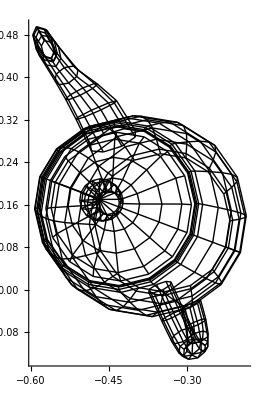

```mathematica
Graphics[Line[project[#,0.0,0.0,2.0]]&/@Rescale[linePts],Axes->True,PlotRange->All]
```

```mathematica
Graphics[GraphicsComplex[f[vertices],Line/@lines],Axes->True,PlotRange->All]
```

```mathematica
Manipulate[Graphics[{Thickness[0.025],Red,Line[Perspective[Trans[RotFigure[Cube,a,b,c],0,0,-3],-1]]},PlotRange->{{-0.7,0.7},{-0.7,0.7}},ImageSize->1.1 {400,400}],
{{a,0},0,2*3.1416,.0001,Appearance->"Labeled"},
{{b,0},0,2*3.1416,.0001,Appearance->"Labeled"},
{{c,0},0,2*3.1416,.0001,Appearance->"Labeled"}
]
```